### Start choosing the example:

```mathematica
t=26;
```

```mathematica
beta =0;
A=.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
MFGEquations=DataToEquations[Data];//Timing
v0={MFGEquations["jvars"],MFGEquations["jtvars"],MFGEquations["uvars"]}/.MFGEquations["criticalreduced1"][[2]]
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 1.×10^-6 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.00754,Null}

{<|{2,1->2}→80.,{ex2503,2->ex2503}→80.,{1,en2502->1}→80.,{1,1->2}→0.,{2,2->ex2503}→0.,{en2502,en2502->1}→0.|>,<|{1,1->2,en2502->1}→0.,{1,en2502->1,1->2}→80.,{2,1->2,2->ex2503}→80.,{2,2->ex2503,1->2}→0.|>,<|{1,1->2}→95.,{2,2->ex2503}→15.,{en2502,en2502->1}→95.,{2,1->2}→15.,{ex2503,2->ex2503}→15.,{1,en2502->1}→95.|>}

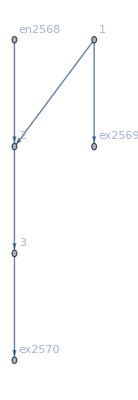

```mathematica
MFGEquations["FG"]
```

#### Non-linear case

```mathematica
alpha =1;FFR=FixedPoint[FixedReduceX1[MFGEquations], MFGEquations["criticalreduced1"][[2]],6, SameTest-> (Norm[(KeySort@#1-KeySort@#2)//Values]<10^(-17)&)];
MFGEquations["jvars"]/.FFR
MFGEquations["jtvars"]/.FFR
MFGEquations["uvars"]/.FFR
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.57009×10^-15

<|{2,1->2}→0.,{ex2569,1->ex2569}→1.,{3,2->3}→1.,{ex2570,3->ex2570}→1.,{2,en2568->2}→2.,{1,1->2}→1.,{1,1->ex2569}→0.,{2,2->3}→0.,{3,3->ex2570}→0.,{en2568,en2568->2}→0.|>

<|{1,1->2,1->ex2569}→1.,{1,1->ex2569,1->2}→0.,{2,1->2,2->3}→0.,{2,1->2,en2568->2}→0.,{2,2->3,1->2}→0.,{2,2->3,en2568->2}→0.,{2,en2568->2,1->2}→1.,{2,en2568->2,2->3}→1.,{3,2->3,3->ex2570}→1.,{3,3->ex2570,2->3}→0.|>

<|{1,1->2}→5.,{1,1->ex2569}→5.,{2,2->3}→6.,{3,3->ex2570}→5.,{en2568,en2568->2}→6.,{2,1->2}→6.,{ex2569,1->ex2569}→5.,{3,2->3}→5.,{ex2570,3->ex2570}→5.,{2,en2568->2}→6.|>